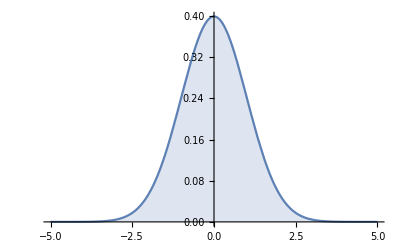

```mathematica
(* some numerical experiments with thin and fat tailed distributions *)

dist01=NormalDistribution[0,1];
Pdist01=PDF[dist01,x];
Plot[Pdist01,{x,-5,5}, Filling->Axis]
```

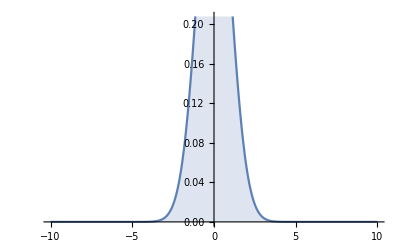

```mathematica
Plot[Pdist01,{x,-10,10}, Filling->Axis]
```

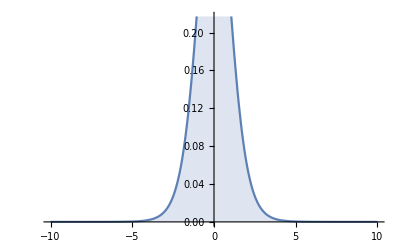

```mathematica
dist02=StudentTDistribution[0,1,10];
Pdist02=PDF[dist02,x];
Plot[Pdist02,{x,-10,10}, Filling->Axis]
```

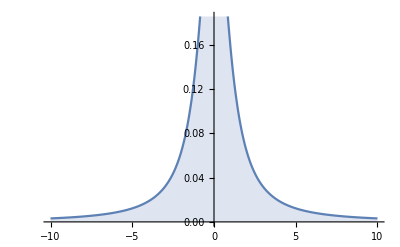

```mathematica
dist03=CauchyDistribution[0,1];
Pdist03=PDF[dist03,x];
Plot[Pdist03,{x,-10,10}, Filling->Axis]
```

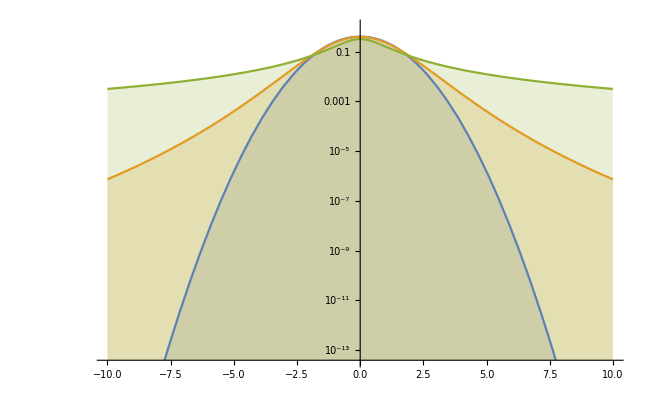

```mathematica
LogPlot[{Pdist01,Pdist02,Pdist03},{x,-10,10}, Filling->Axis]
```

TemporalData[…]

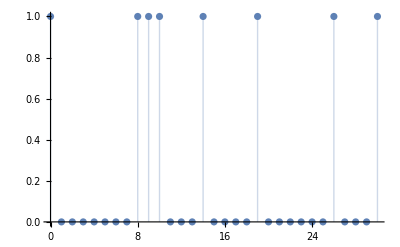

```mathematica
data01=RandomFunction[BernoulliProcess[0.3],{0,30}]
ListPlot[data01,Filling->Axis]
```

```mathematica
Mean[BernoulliProcess[p][t]]
```

p

TemporalData[…]

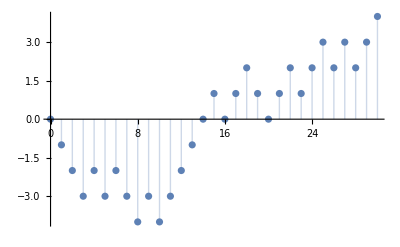

```mathematica
data02=RandomFunction[RandomWalkProcess[.5],{0,30}]
ListPlot[data02,Filling->Axis]
```

```mathematica
Mean[RandomWalkProcess[p][t]]
```

(-1+2 p) t

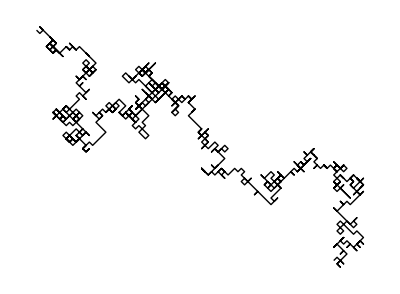

```mathematica
SeedRandom[2017];
data02d=RandomFunction[RandomWalkProcess[0.5],{0,10^3},2];
Graphics[Line[Transpose@data02d["ValueList"]],AspectRatio->Automatic]
```

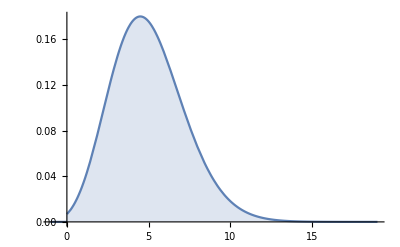

```mathematica
dist04=PoissonDistribution[5];
Pdist04=PDF[dist04,x];
Plot[Pdist04,{x,-1,19}, Filling->Axis]
```

TemporalData[…]

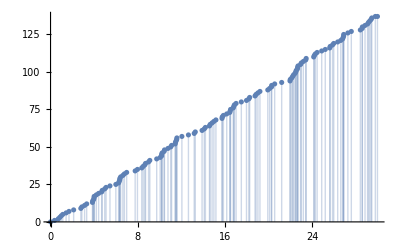

```mathematica
data04=RandomFunction[PoissonProcess[5],{0,30}]
ListPlot[data04,Filling->Axis]
```

```mathematica
Mean[PoissonProcess[μ][t]]
```

t μ

TemporalData[…]

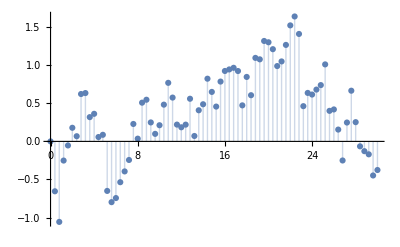

```mathematica
data05=RandomFunction[WienerProcess[0.0,0.5],{0,30,0.4}]
ListPlot[data05,Filling->Axis]
```

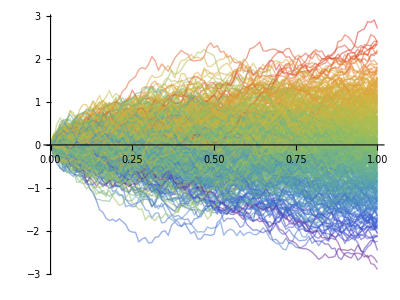

```mathematica
data06=RandomFunction[WienerProcess[],{0,1,.01},500];
slice06=data06["SliceData",1];
cf=ColorData["Rainbow"];
ListLinePlot[data06,ImageSize->400,PlotRange->All,AspectRatio->3/4,BaseStyle->Directive[Thin,Opacity[0.5]],PlotStyle->(cf/@Rescale[slice06]),PlotRangePadding->{{0,.25},{.5,.5}}]
```

```mathematica
Mean[WienerProcess[μ,σ][t]]
Variance[WienerProcess[μ,σ][t]]
```

t μ

t σ^2